# Continuous Versus Discrete Logistic Growth

Adam Rumpf, 11/4/2014

## Introduction

This demonstration is meant to compare the continuous and the discrete versions of the logistic growth model. Both are population models which cause the population to be limited due to limited resources. The continuous model is usually given by the ODE

```mathematica
ⅆx/ⅆt=r x(L-x)
```

where x is the population as a function of time t, r>1 is the intrinsic growth rate, and L is the carrying capacity. Notice that this equation results in ⅆx/ⅆt>0 when 0<x<L and ⅆx/ⅆt<0 when x>L, meaning that the population should grow while below L and shrink while above L, which is how the carrying capacity is enforced.

The discrete analog of this model is usually given as the discrete logistic map

x_(n+1)=r x_n(1-x_n)

where x_n is the population at time step n, r>1 is again the intrinsic growth rate, and we generally assume that the population units have been scaled so that the carrying capacity can be stated as 1. Note, however, that 1 is not actually the equilibrium solution of this system: solving x^*=r x^*(1-x^*) yields the (nonzero) equilibrium solution as x^*=(r-1)/r.

The figures below show how these two models behave side-by-side as r changes. In order to remove the potential confusion of the continuous model having a constant equilibrium while the discrete model does not, we will always rescale the continuous model so that L=(r-1)/r, meaning that both models will always have the same carrying capacity.

## Code

### Initialization

```mathematica
logfinal[x0_,r_,lim_,end_]:=Partition[Riffle[ConstantArray[r,end],RecurrenceTable[{x[n+1]==r x[n](1-x[n]),x[0]==x0},x,{n,0,lim}][[-end;;]]],2]
```

```mathematica
dlmplot=Flatten[Table[logfinal[0.4,r,100,20],{r,1.005,4,0.005}],1];
```

### Demonstration

We begin by showing a time series of population versus time for both models. Try gradually increasing r from 1 all the way to 4. At first the two models should produce nearly identical behavior, but after r≥2 the discrete version should begin to produce oscillations which the continuous model does not. This is because the discrete model allows the carrying capacity to be slightly overshot between iterations, after which we must experience negative growth. The overshooting goes on for several iterations before dying down.

After r≥3 the growth rate is large enough that the oscillations no longer die down and instead remain as periodic orbits. Increasing r even further beyond this point causes the orbits to increase in period, from 2 to 4 and then 8 and so on, until for very large values of r the results are completely chaotic.

```mathematica
Manipulate[TableForm[{{Plot[Evaluate[(E^(L r t)L 0.4)/(L+(E^(L r t)-1)0.4)/.L->(r-1)/r],{t,0.001,30},PlotRange->{0,1},PlotLabel->"continuous",AxesLabel->{"t","x(t)"}],ListPlot[RecurrenceTable[{x[n+1]==r x[n](1-x[n]),x[0]==0.4},x,{n,0,30}],Joined->True,Mesh->Full,PlotRange->{0,1},PlotLabel->"discrete",AxesLabel->{"t","x(t)"}]}}],{{r,1.2},1.0005,4,0.0005}]
```

Below is a pair of static plots for any and all long-term behaviours of each model as a function of r. If the model converges to a single equilibrium, then that equilibrium value is plotted as a point, while if the model oscillates indefinitely, all points in the periodic orbit are plotted. As expected from the above observations, the continuous model only ever produces a single equilibrium value, while the discrete model does at first, but then after r≥3 begins to divide into multiple values due to oscillation, and for the largest values of r the plot is an indiscernible cloud of seemingly random points.

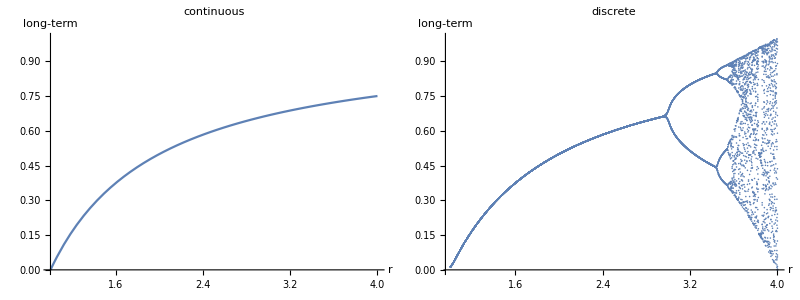

```mathematica
TableForm[{{Plot[(r-1)/r,{r,1.0005,4},PlotRange->{0,1},PlotLabel->"continuous",AxesLabel->{"r","long-term"}],ListPlot[dlmplot,PlotRange->{0,1},PlotLabel->"discrete",AxesLabel->{"r","long-term"}]}}]
```

The following two Manipulate environments are interactive versions of the above observations. The first shows the continuous model’s time series alongside its long-term solutions, both as r changes, and the second shows the same for the discrete model. For the discrete model, observe how the long-term series begins to split just as the time series begins to experience undamped oscillation.

```mathematica
Manipulate[TableForm[{{Plot[Evaluate[(E^(L r t)L 0.4)/(L+(E^(L r t)-1)0.4)/.L->(r-1)/r],{t,0.001,30},PlotRange->{0,1},PlotLabel->"continuous",AxesLabel->{"t","x(t)"}],Plot[(rr-1)/rr,{rr,1.0005,r},PlotRange->{{1,4},{0,1}},PlotLabel->"continuous",AxesLabel->{"r","long-term"}]}}],{{r,1.2},1.005,4,0.005}]
```

```mathematica
Manipulate[TableForm[{{ListPlot[RecurrenceTable[{x[n+1]==r x[n](1-x[n]),x[0]==0.4},x,{n,0,30}],Joined->True,Mesh->Full,PlotRange->{0,1},PlotLabel->"discrete",AxesLabel->{"t","x(t)"}],ListPlot[dlmplot[[1;;20(Round[(r-1.005)/0.005]+1)]],PlotRange->{{1,4},{0,1}},PlotLabel->"discrete",AxesLabel->{"r","long-term"}]}}],{{r,1.2},1.005,4,0.005}]
```